```mathematica
Solve[{0==-kf*L*Rs+kr*Rst-ke*Rs+Vs,0==kf*L*Rs-kr*Rst-kest*Rst,L==(q*nc+kr*Rst*nc)/(km+kf*Rs*nc)},{Rst,Rs,L}]//FullSimplify
```

{{Rst→1/(2 kest^2 kf nc)(ke km (kest+kr)+kest kf nc (q+Vs)+√((ke km (kest+kr)+kest kf nc (q-Vs))^2+4 ke kest kf km (kest+kr) nc Vs)),Rs→-1/(2 ke kest kf nc)(ke km (kest+kr)+kest kf nc (q-Vs)+√((ke km (kest+kr)+kest kf nc (q-Vs))^2+4 ke kest kf km (kest+kr) nc Vs)),L→-1/(2 kest kf km)(ke km (kest+kr)+kest kf nc (-q+Vs)+√((ke km (kest+kr)+kest kf nc (q-Vs))^2+4 ke kest kf km (kest+kr) nc Vs))},{Rst→1/(2 kest^2 kf nc)(ke km (kest+kr)+kest kf nc (q+Vs)-√((ke km (kest+kr)+kest kf nc (q-Vs))^2+4 ke kest kf km (kest+kr) nc Vs)),Rs→1/(2 ke kest kf nc)(-ke km (kest+kr)+kest kf nc (-q+Vs)+√((ke km (kest+kr)+kest kf nc (q-Vs))^2+4 ke kest kf km (kest+kr) nc Vs)),L→1/(2 kest kf km)(-ke km (kest+kr)+kest kf nc (q-Vs)+√((ke km (kest+kr)+kest kf nc (q-Vs))^2+4 ke kest kf km (kest+kr) nc Vs))}}

```mathematica
ke=10^-4;
kest=5*10^-3;
kf=5.14*10^-21;
kr=2.5*10^-2;
kdeg=8*10^-4;
Vs=18;
q=10^3;
nc=3*10^8;
γ=10^2;
DL=10^-10;
km=DL/z((γ*z^2)/DL)^(1/3);
```

```mathematica
L=1/(2 kest kf km)(-ke km (kest+kr)+kest kf nc (q-Vs)+√((ke km (kest+kr)+kest kf nc (q-Vs))^2+4 ke kest kf km (kest+kr) nc Vs));
```

```mathematica
Kss=(kest*kf)/(ke(kr+kest));
```

```mathematica
Rstt=(1/kest+1/kdeg)*Kss*Vs*L//FullSimplify
```

-13050.+(z (32934.8+4.35×10^15 √(5.73234×10^-23+(4.70927×10^-23 z)/((z^2)^(2/3))+(9.×10^-24)/((z^2)^(1/3)))))/((z^2)^(1/3))

The mitotic activity will follow the above profile and would be scaled by the proportionality constant, mitogenic signal(γ) which arises from transpot and signal transduction: mitotic activity=γ*R_total^*

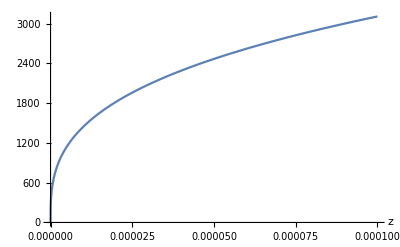

```mathematica
Plot[Rstt,{z,0,.0001},AxesLabel->Automatic,PlotRange->All]
```